```mathematica
SetDirectory[NotebookDirectory[]]
```

## First set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_S_data_1.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{2715,2}

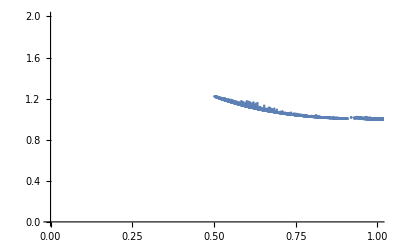

```mathematica
ListPlot[rawdata,PlotRange->{{0,1},{0,2}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{1.2727,1.11316}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{106,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

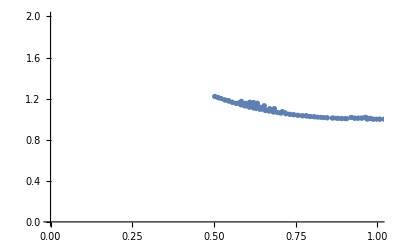

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,1},{0,2}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_S_densADJ_1.txt",densADJrescaled, "Table"]
```

## Second set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_S_data_2.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{23324,2}

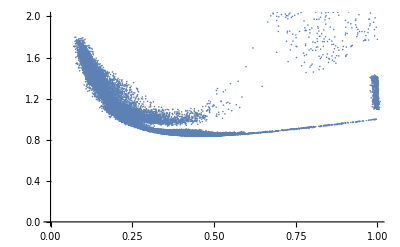

```mathematica
ListPlot[rawdata,PlotRange->{{0,1},{0,2}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.825542,0.846727}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{865,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

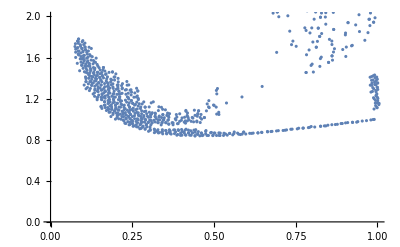

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,1},{0,2}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_S_densADJ_2.txt",densADJrescaled, "Table"]
```

## Third set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_S_data_3.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{4078,2}

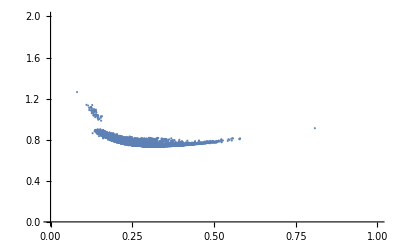

```mathematica
ListPlot[rawdata,PlotRange->{{0,1},{0,2}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.311342,0.857041}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{192,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

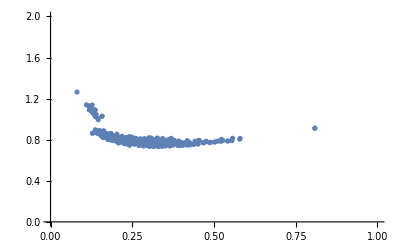

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,1},{0,2}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_S_densADJ_3.txt",densADJrescaled, "Table"]
```

## Fourth set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_S_data_4.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{12805,2}

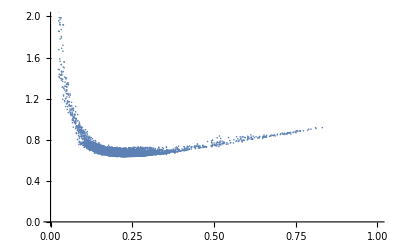

```mathematica
ListPlot[rawdata,PlotRange->{{0,1},{0,2}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.35602,0.706379}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,23324}];
```

```mathematica
Dimensions[densADJ]
```

{418,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

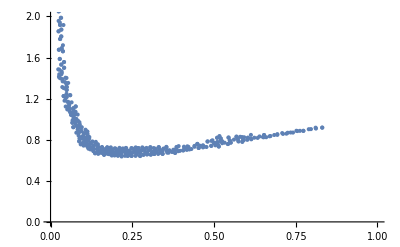

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,1},{0,2}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_S_densADJ_4.txt",densADJrescaled, "Table"]
```

## Fifth set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_S_data_5.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{19303,2}

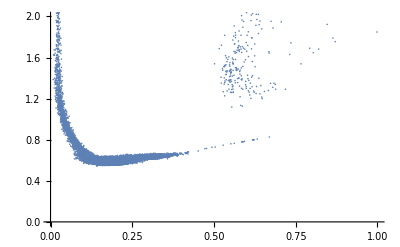

```mathematica
ListPlot[rawdata,PlotRange->{{0,1},{0,2}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.37945,0.562559}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{479,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

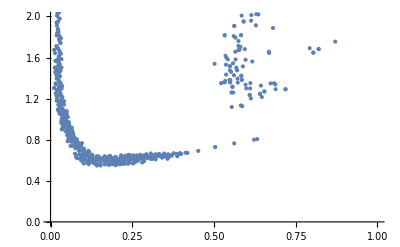

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,1},{0,2}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_S_densADJ_5.txt",densADJrescaled, "Table"]
```

## Sixth set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_S_data_6.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{16007,2}

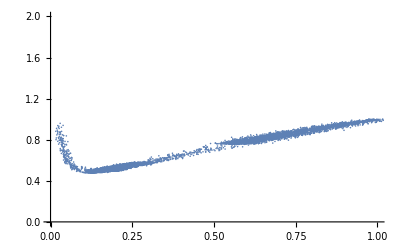

```mathematica
ListPlot[rawdata,PlotRange->{{0,1},{0,2}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.321124,0.501582}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{386,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

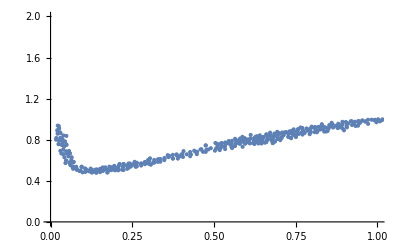

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,1},{0,2}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_S_densADJ_6.txt",densADJrescaled, "Table"]
```

## Seventh set

```mathematica
rawdata = Import["DataForPlotting\\SI_CV_vs_S_data_7.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{30602,2}

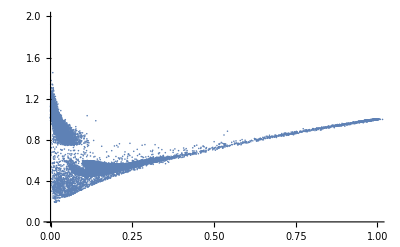

```mathematica
ListPlot[rawdata,PlotRange->{{0,1},{0,2}}]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.02}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.280338,0.53106}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,10000}];
```

```mathematica
Dimensions[densADJ]
```

{632,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

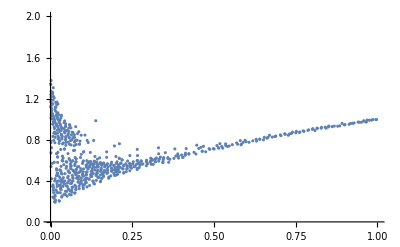

```mathematica
ListPlot[densADJrescaled,PlotRange->{{0,1},{0,2}}]
```

```mathematica
Export["DataForPlotting\\SI_CV_vs_S_densADJ_7.txt",densADJrescaled, "Table"]
```